# FEW vs WaSABI 1PAT1R Implementation

#### Python setup. PySaBI? FEWSaBI

Executing python from within conda environment “1pat1r” having installed FEW- edit path to your own executable.

```mathematica
session=StartExternalSession[<|"System"->"Python","Executable"->"/Users/joshmathews/anaconda3/envs/1pat1r/bin/python"|>];
```

```mathematica
py=ExternalEvaluate[session];
```

## Comparing the amplitudes against WaSABI

#### Getting FEW amplitudes:

Importing stuff

```mathematica
py["from few.trajectory.inspiral import EMRIInspiral"];
py["from few.trajectory.ode.IPAT1R import Trajectory1PAT1R"];
py["import matplotlib.pyplot as plt"];
py["import numpy as np"];
py["from few.amplitude.ampinterp1d import AmpInterp1PAT1R"];
py["amp = AmpInterp1PAT1R()"]
```

Evaluating the amplitude pieces

```mathematica
GetAmpsAtr0[r0_,l_,m_]:=Module[{string,amps0PA,amps1PA,ampschi2,ampschi1,ampsdeltam,pos},
pos=Flatten[Position[Flatten[Table[{ll,mm},{ll,2,5},{mm,1,ll}],1],{l,m}]][[1]];
string="amp.get_amplitudes_single_piece(0,"<>ToString[r0]<>", 0.0, 1.0,";
amps0PA=Flatten[Normal[py[string<>"data_key=\"0PA\")"]]][[5;;]][[pos]];
amps1PA=Flatten[Normal[py[string<>"data_key=\"1PA\")"]]][[5;;]][[pos]];
ampschi2=Flatten[Normal[py[string<>"data_key=\"1PAchi2\")"]]][[5;;]][[pos]];
ampschi1=Flatten[Normal[py[string<>"data_key=\"1PAchi1\")"]]][[5;;]][[pos]];
ampsdeltam=Flatten[Normal[py[string<>"data_key=\"1PAdeltam\")"]]][[5;;]][[pos]];
<|"0PA"->amps0PA,"1PA"->amps1PA,"chi2"->ampschi2,"chi1"->ampschi1,"δm"->ampsdeltam|>
]
```

```mathematica
GetAmpsAtr0[7.0,2,1]
```

<|0PA→-0.0339536-0.121127 ⅈ,1PA→0.0521078+0.26001 ⅈ,chi2→-0.0101694-0.036284 ⅈ,chi1→0.0231815+0.0834066 ⅈ,δm→-0.0578894-0.134309 ⅈ|>

```mathematica
GetAmpsAtr0Combined[r0_,l_,m_,ν_,chit1_,chit2_,deltam1_]:=Module[{modestring,string1},
py["nu="<>ToString[ν]];
py["chit1="<>ToString[chit1]];
py["chit2="<>ToString[chit2]];
py["delta_m1="<>ToString[deltam1]];
modestring="("<>ToString[l]<>","<>ToString[m]<>",0,0)";
string1="amp.get_amplitudes(0,"<>ToString[r0]<>", 0.0, 1.0, nu=nu, chit=chit1,chit2=chit2, delta_m1=delta_m1,specific_modes=["<>modestring<>"])["<>modestring<>"]";
Normal[py[string1]]
]
```

```mathematica
GetAmpsAtr0Combined[7.0,2,2,0.1,0.5,0.5,0.6]
```

{0.747372-0.293311 ⅈ}

#### Getting WaSABI amplitudes

```mathematica
<<WaSABI`
```

```mathematica
GetWaSABIAmps[r0_,l_,m_]:=Module[{fullamp,modestring,amps0PA,amps1PA,ampschi2,ampschi1,ampsdeltam},
modestring="("<>ToString[l]<>","<>ToString[m]<>")";
fullamp=If[OddQ[m],1/(√(1-4ν))(*Accounting for resummed odd amp vs raw data*)(WaSABI`Waveform`Private`GetAmplitudes["1PAT1R",{}]/.{ WaSABI`Inspiral`Model1PAT1R`ν->ν,WaSABI`Inspiral`Model1PAT1R`Ω->√(1/r0^3),WaSABI`Inspiral`Model1PAT1R`M->1,WaSABI`Inspiral`Model1PAT1R`χt1->χt1,WaSABI`Inspiral`Model1PAT1R`χt2->χt2,WaSABI`Inspiral`Model1PAT1R`δm->δm})[modestring],(WaSABI`Waveform`Private`GetAmplitudes["1PAT1R",{}]/.{ WaSABI`Inspiral`Model1PAT1R`ν->ν,WaSABI`Inspiral`Model1PAT1R`Ω->√(1/r0^3),WaSABI`Inspiral`Model1PAT1R`M->1,WaSABI`Inspiral`Model1PAT1R`χt1->χt1,WaSABI`Inspiral`Model1PAT1R`χt2->χt2,WaSABI`Inspiral`Model1PAT1R`δm->δm})[modestring]];
amps0PA=Coefficient[fullamp,ν]/.{χt1->0,χt2->0};
amps1PA=If[OddQ[m],(Coefficient[fullamp,ν^2]/.{χt1->0,χt2->0,δm->0})-2*amps0PA,(Coefficient[fullamp,ν^2]/.{χt1->0,χt2->0,δm->0})];
ampschi1=Coefficient[fullamp,χt1]/.{ν->1};
ampschi2=Coefficient[fullamp,χt2]/.{ν->1};
ampsdeltam=Coefficient[fullamp,δm]/.{ν->1};
<|"0PA"->amps0PA,"1PA"->amps1PA,"chi2"->ampschi2,"chi1"->ampschi1,"δm"->ampsdeltam|>
]
```

```mathematica
GetWaSABIAmpsCombined[r0_,l_,m_]:=Module[{fullamp,modestring},
modestring="("<>ToString[l]<>","<>ToString[m]<>")";
fullamp=(WaSABI`Waveform`Private`GetAmplitudes["1PAT1R",{}]/.{ WaSABI`Inspiral`Model1PAT1R`ν->ν,WaSABI`Inspiral`Model1PAT1R`Ω->√(1/r0^3),WaSABI`Inspiral`Model1PAT1R`M->1,WaSABI`Inspiral`Model1PAT1R`χt1->χt1,WaSABI`Inspiral`Model1PAT1R`χt2->χt2,WaSABI`Inspiral`Model1PAT1R`δm->δm})[modestring]
]
```

#### Comparisons of individual amplitude terms --- See only 1PA (5,1) mode being noteworthy.

```mathematica
1-GetWaSABIAmps[7.0,2,2]/(-GetAmpsAtr0[7.0,2,2])
```

<|0PA→-4.17752×10^-9-3.18693×10^-9 ⅈ,1PA→-1.43976×10^-7-5.50014×10^-7 ⅈ,chi2→-2.48211×10^-8-6.00775×10^-9 ⅈ,chi1→-6.11024×10^-8-2.47188×10^-9 ⅈ,δm→-1.04262×10^-6-9.21362×10^-7 ⅈ|>

```mathematica
ampcheck[l_,m_]:=Table[{r0,Abs[1-GetWaSABIAmps[r0,l,m]/(-GetAmpsAtr0[r0,l,m])]},{r0,6.25,30,0.01}]
```

```mathematica
Monitor[Do[amprelerr[l,m]=ampcheck[l,m];,{l,2,5},{m,1,l}],{l,m}]
```

```mathematica
keys=Keys[amprelerr[2,2][[1,2]]];
Do[
series[l,m]=Table[{key,Table[{row[[1]],row[[2]][key]},{row,amprelerr[l,m]}]},{key,keys}];,{l,2,5},{m,1,l}]
```

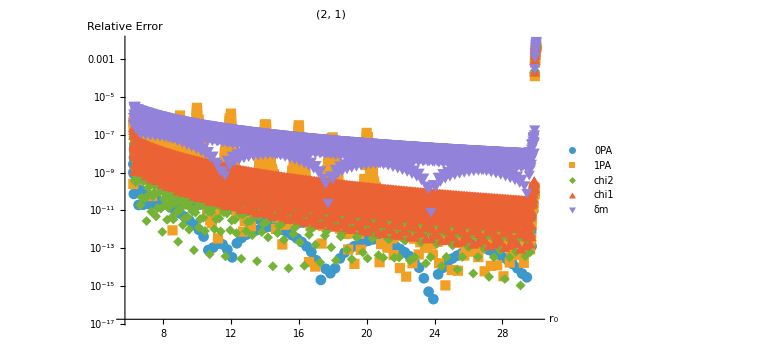

```mathematica
With[{l=2,m=1},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

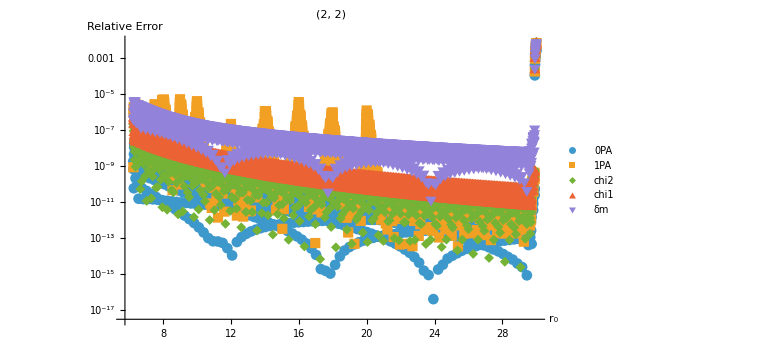

```mathematica
With[{l=2,m=2},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

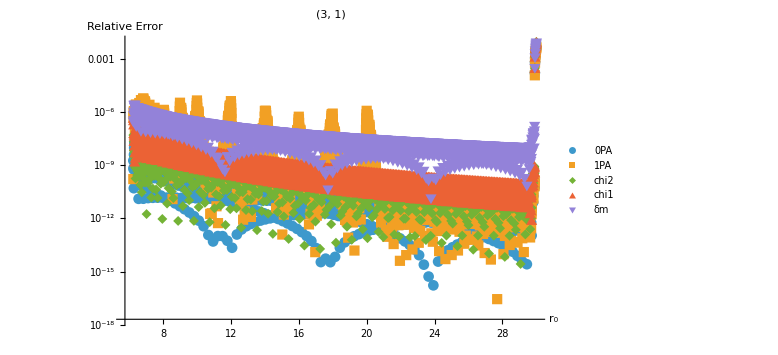

```mathematica
With[{l=3,m=1},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

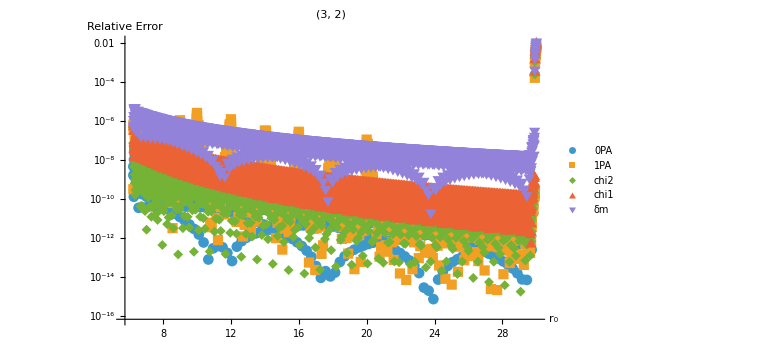

```mathematica
With[{l=3,m=2},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

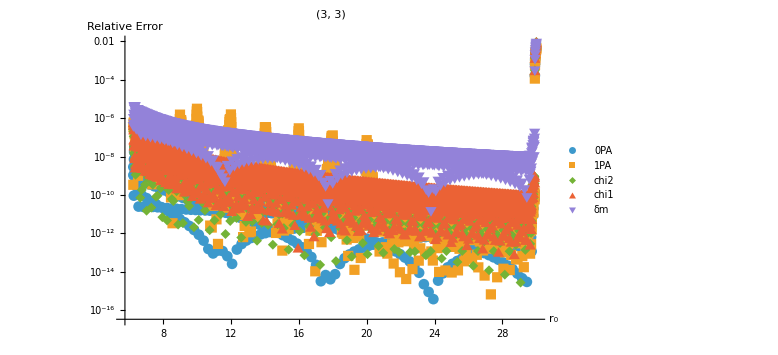

```mathematica
With[{l=3,m=3},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

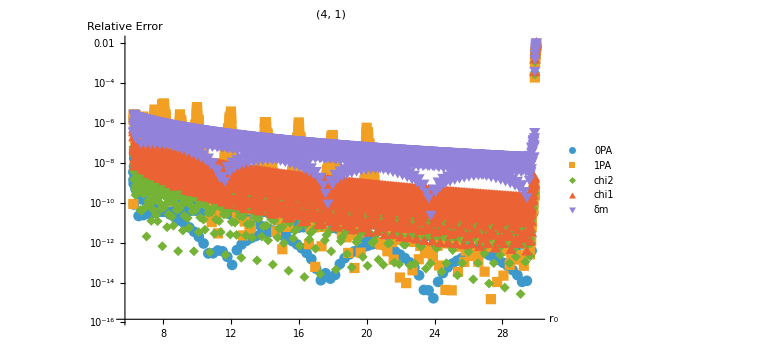

```mathematica
With[{l=4,m=1},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

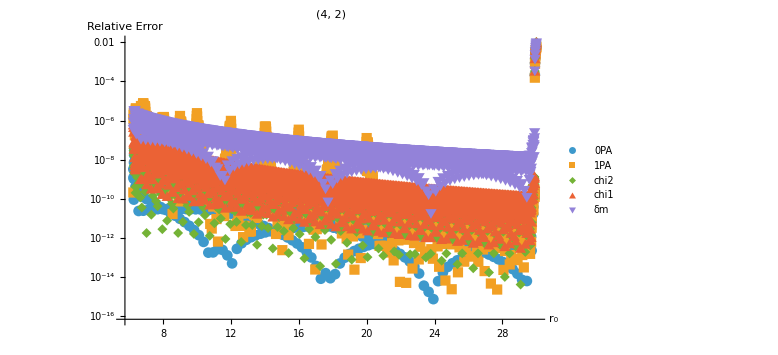

```mathematica
With[{l=4,m=2},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

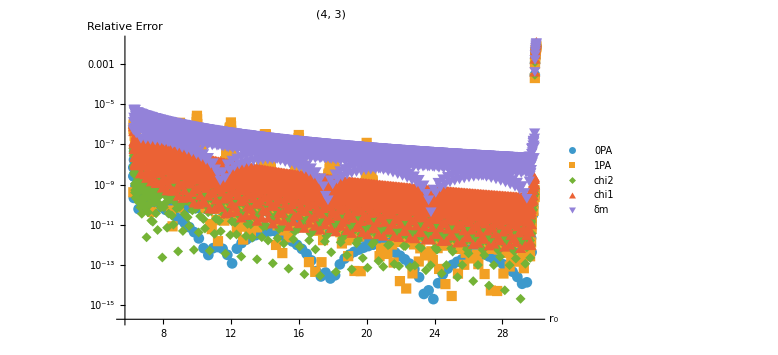

```mathematica
With[{l=4,m=3},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

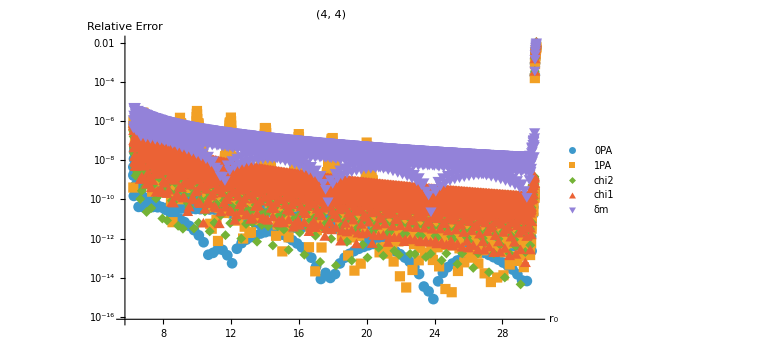

```mathematica
With[{l=4,m=4},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

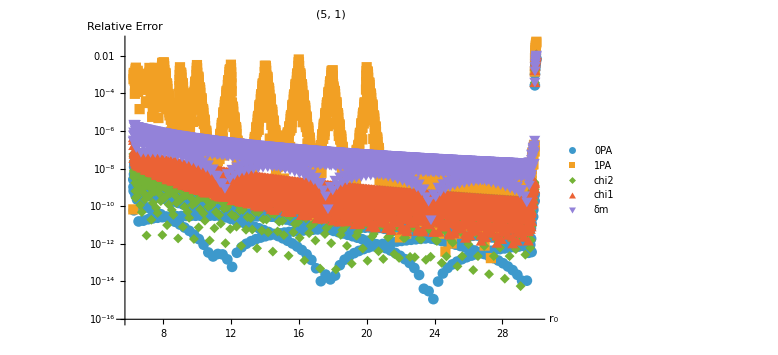

```mathematica
With[{l=5,m=1},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

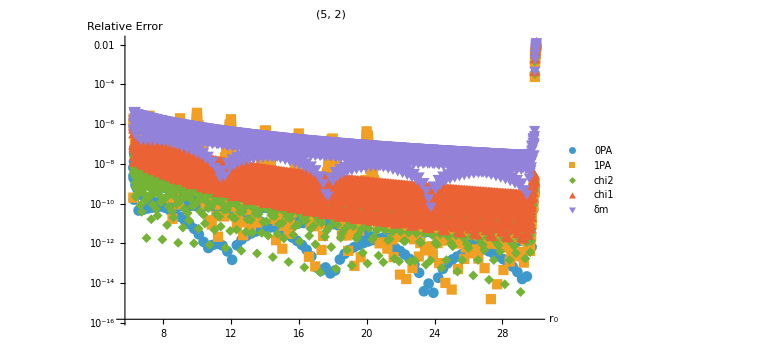

```mathematica
With[{l=5,m=2},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

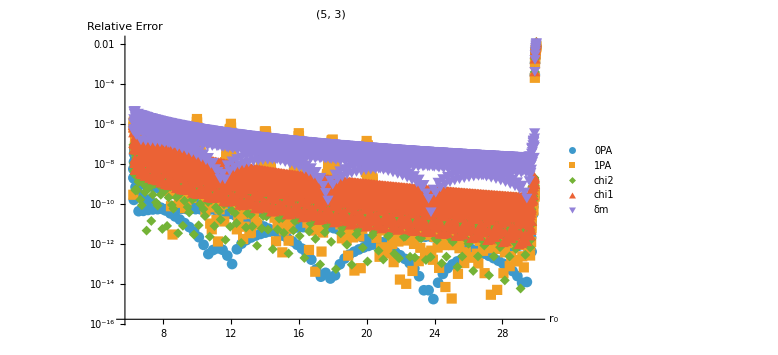

```mathematica
With[{l=5,m=3},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

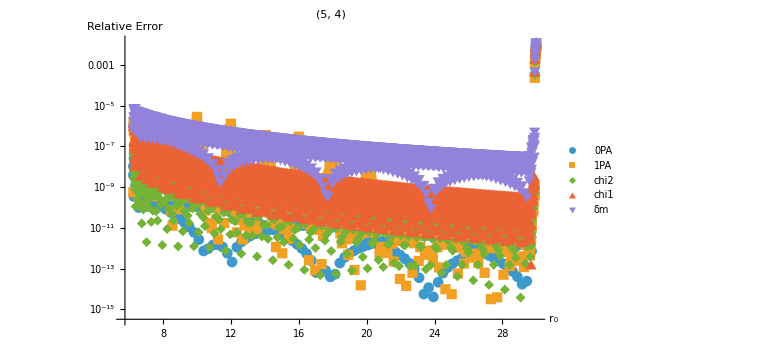

```mathematica
With[{l=5,m=4},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

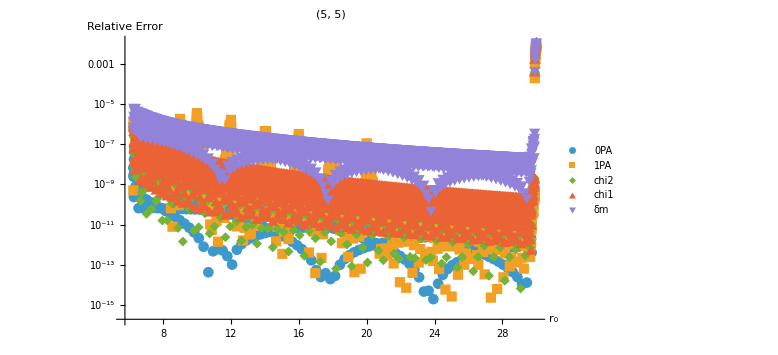

```mathematica
With[{l=5,m=5},ListLogPlot[series[l,m][[All,2]],PlotLegends->keys,Joined->False,PlotMarkers->Automatic,AxesLabel->{"r_0","Relative Error"},ImageSize->Large, PlotLabel->"("<>ToString[l]<>", "<>ToString[m]<>")"]]
```

#### Comparison of combined amplitudes

```mathematica
GetWaSABIAmpsCombined[7.0,2,2]/.{ν->0.1,χt1->0.5,χt2->0.5,δm->0.6}
```

-0.0747372+0.0293311 ⅈ

Note few amplitudes scale waveform by ν:

```mathematica
combinecheckWasabi=(1/ν)GetWaSABIAmpsCombined[7.0,2,1]/.{ν->0.1,χt1->0.5,χt2->0.5,δm->0.6}
```

0.0251751+0.0804409 ⅈ

```mathematica
combinecheckFEW=-GetAmpsAtr0Combined[7.0,2,1,0.1,0.5,0.5,0.6]
```

{0.0251751+0.0804408 ⅈ}

```mathematica
1-(combinecheckWasabi/combinecheckFEW)
```

{-1.01054×10^-7+2.26312×10^-8 ⅈ}

```mathematica
combinecheckWasabi2=(1/ν)GetWaSABIAmpsCombined[7.0,2,1]/.{ν->0.1,χt1->-0.5,χt2->0.5,δm->0.6}
```

0.0431314+0.145047 ⅈ

```mathematica
combinecheckFEW2=-GetAmpsAtr0Combined[7.0,2,1,0.1,-0.5,0.5,0.6]
```

{0.0431314+0.145047 ⅈ}

```mathematica
1-(combinecheckWasabi2/combinecheckFEW2)
```

{-6.70036×10^-8+1.52379×10^-8 ⅈ}

So we have checked the individual interpolations and that the amplitudes are combined correctly.

## Comparing the inspiral against WaSABI

Put me here.

## Comparing the waveform against WaSABI

Put me here.